```mathematica
SetDirectory[NotebookDirectory[]];
Nc=3.;
mf2[h_,ρ_]:=(h^2 ρ)/2;
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
F1[q_,ρ_,h_,T_,μ_]:=q^2/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^2/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(h^2 Nc)/(2π)^2 NIntegrate[(2F1[q,ρ,h,T,μ]-(p0^2+ps^2)Re[F1F1m[q,p0,ps,x,ρ,h,T,μ]]),{q,0.,10.,20.,30.,40.,50.,100.,500.,5000.},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->50,WorkingPrecision->15,AccuracyGoal->10,PrecisionGoal->10];
gammavac[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((*(2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+*)(p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->5])(*-(Nc h^2 mf2[h,ρ])/(16 π^2)*);
gammavac2[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((p0^2+ps^2)/2 NIntegrate[Log[1/MZ^2(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])],{x,0,1},Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->50]);
gamma2[p0_,ps_,ρ_,ρ0_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ]-gammavac2[p0,ps,ρ0,h,Mmass,MZ]+p0^2+ps^2+(λ300 ρ+ν300);
gamma2v1[p0_,ps_,ρ_,ρ0_,h_,T_,μ_,Mmass_,MZ_]:=gamma2thr[p0,ps,ρ,h,T,μ]+gammavac[p0,ps,ρ,h,Mmass,MZ]+p0^2+ps^2+(λ300 ρ+ν300);
λ300=75.8;
ν300=-482.^2;
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

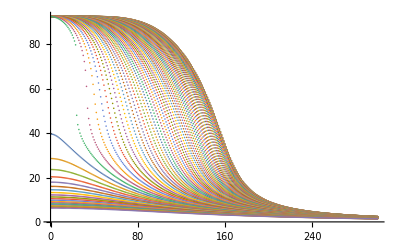

```mathematica
sigmadata=Import["../../../../sigma0.dat"];
ListPlot[sigmadata]
```

```mathematica
muq=Table[i*5,{i,1,80}];
muq[[56]]
muq[[64]]
sigmadata[[1]][[1]]
```

280

320

92.5785

```mathematica
fixM1=ParallelTable[gamma2[0,ps,(sigmadata[[64]][[30]])^2/2,(sigmadata[[1]][[1]])^2/2,6.5,30.,320.,300,300]//Quiet,{ps,1,2001,20}];
```

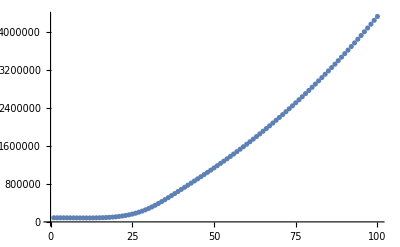

```mathematica
ListPlot[fixM1[[1;;100]]]
```

```mathematica
Export["./Ep.dat",Re[fixM1]];
```

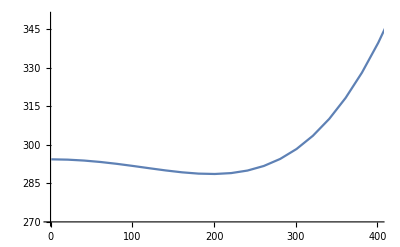

```mathematica
ps=Table[i,{i,1,2001,20}];
ListLinePlot[{Transpose[{ps,√fixM1}]},PlotRange->{{0,400},{270,350}}]
```